## Rapports

### Assymétrie

```mathematica
serie=3;
Module[{dat,datg,datd,assym,normax,normin},
dat=normalizelength[getData[dataproc,serie,"Forward Acceleration (Stroke)"]];
datg=Take[dat,{1,-1,2}];
datd=Take[dat,{2,-1,2}];
datg=Take[datg,Min[Length[datg],Length[datd]]];
datd=Take[datd,Min[Length[datg],Length[datd]]];
assym=Transpose[{Total[Transpose[(datg-datd)^2]],Table[i,{i,Length[datg]}]}];
normax=Max[dat];
normin=Min[dat];
Manipulate[
GraphicsGrid[
{{
ListDensityPlot[datg,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction->Function[{z} ,ColorData["TemperatureMap"][(z-min)/(max-min)]],ColorFunctionScaling->False,DataRange->{{0,100},{0,1000}}],
ListDensityPlot[datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction->Function[{z} ,ColorData["TemperatureMap"][(z-min)/(max-min)]],ColorFunctionScaling->False,DataRange->{{0,100},{0,1000}}]
}}
],{{max,normax},0,10},{{min,normin},-5,0}
]
]
```

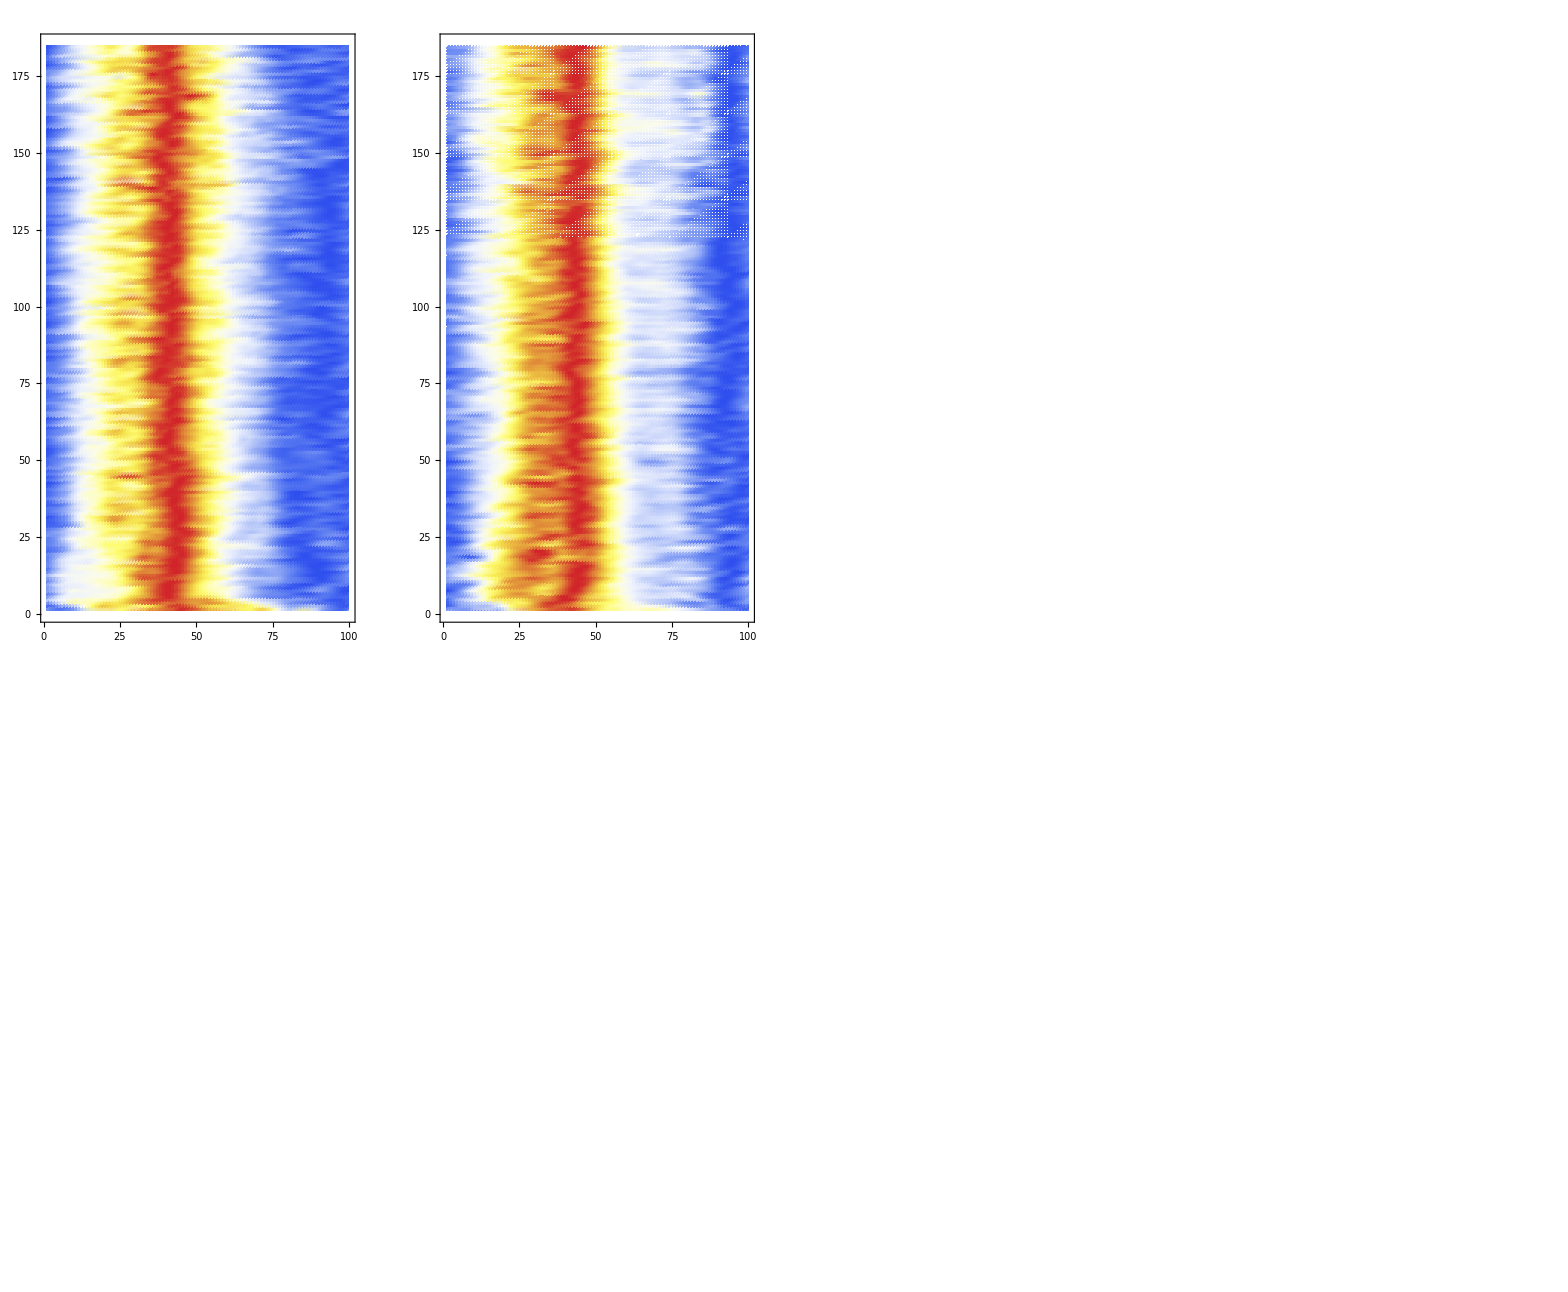

```mathematica
Module[{dat,datg,datd,assym},
dat=normalizeall[getData[dataproc,1,"Forward Acceleration (Stroke)"]];
datg=Take[dat,{1,-1,2}];
datd=Take[dat,{2,-1,2}];
datg=Take[datg,Min[Length[datg],Length[datd]]];
datd=Take[datd,Min[Length[datg],Length[datd]]];
assym=Transpose[{Total[Transpose[(datg-datd)^2]],Table[i,{i,Length[datg]}]}];
GraphicsGrid[
{{
ListDensityPlot[datg,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datg-datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListPlot[assym,ImageSize->{400,600},AspectRatio->Length[ dat]/200,Joined->True]
},
{
ListPlot[Mean[datg],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datd],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datg-datd],ImageSize->{400,400},Joined->True],
0
}}
]
]
```

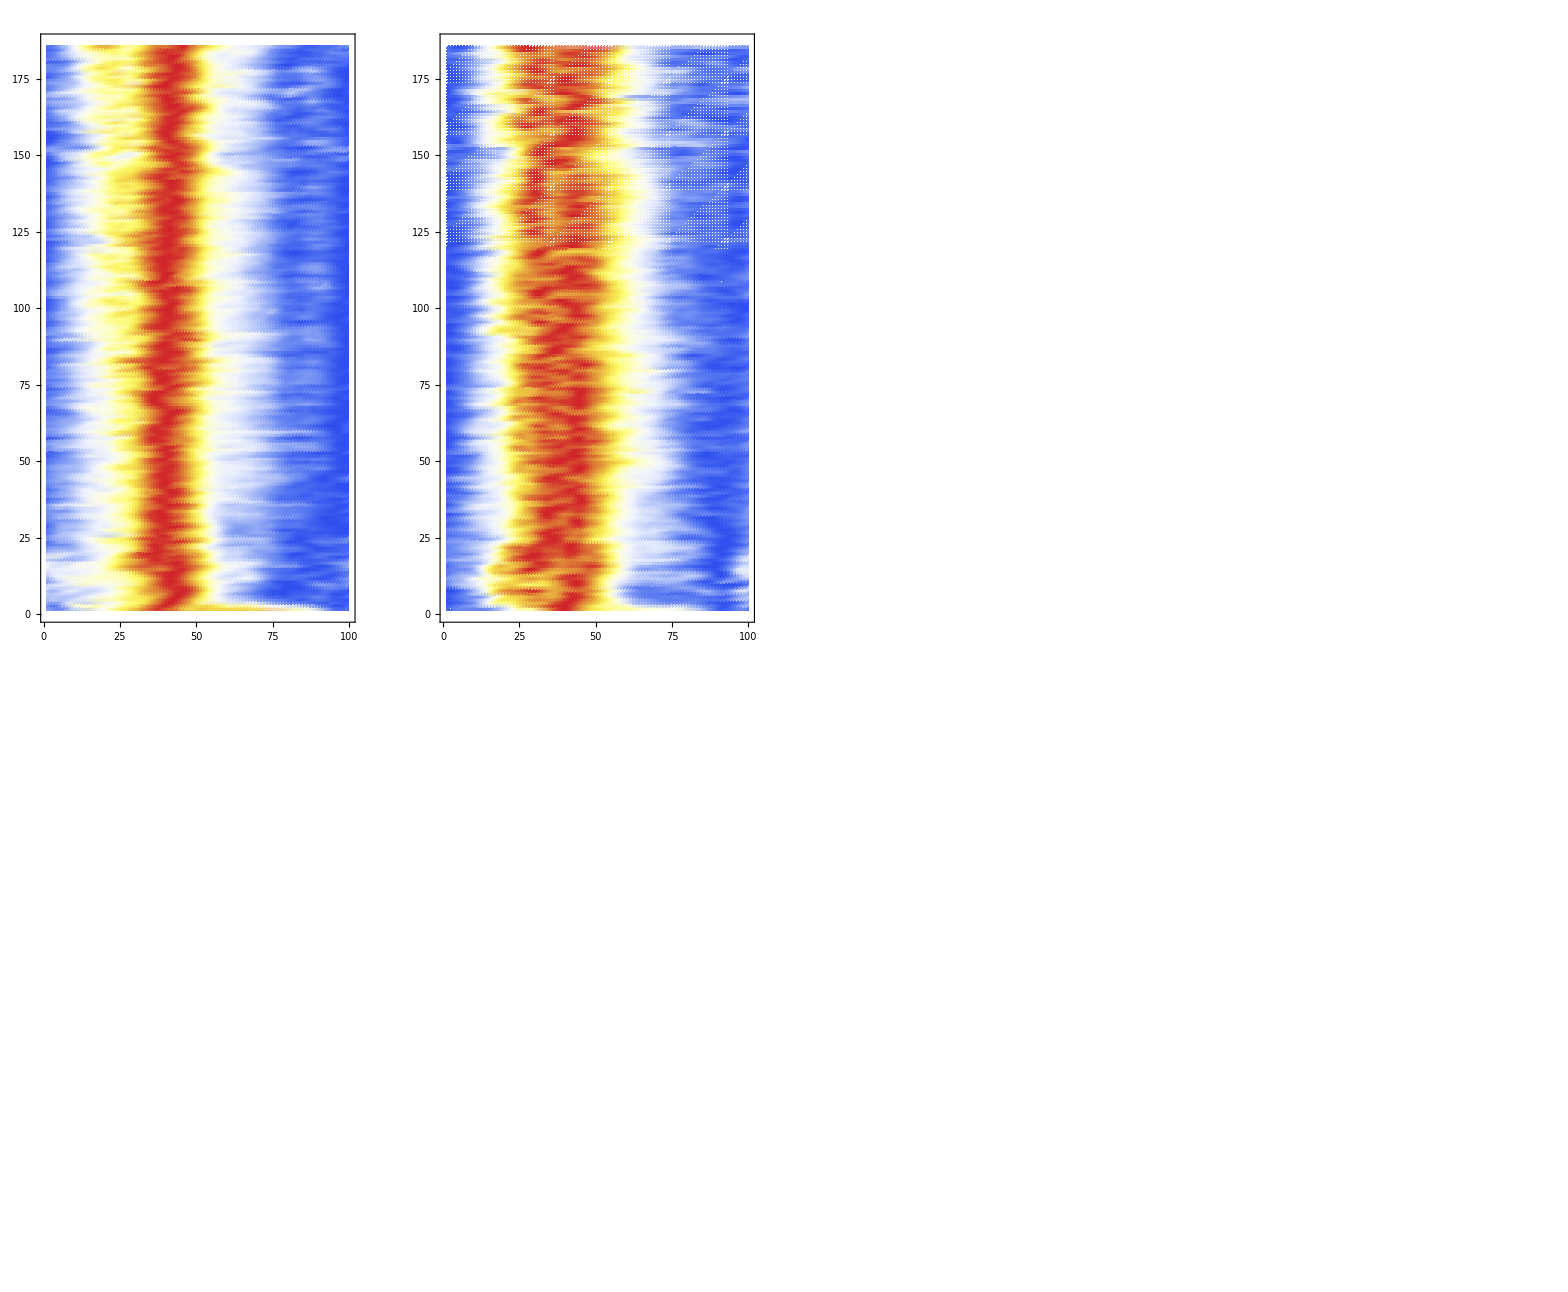

```mathematica
Module[{dat,datg,datd,assym},
dat=normalizeall[getData[dataproc,3,"Forward Acceleration (Stroke)"]];
datg=Take[dat,{1,-1,2}];
datd=Take[dat,{2,-1,2}];
datg=Take[datg,Min[Length[datg],Length[datd]]];
datd=Take[datd,Min[Length[datg],Length[datd]]];
assym=Transpose[{Total[Transpose[(datg-datd)^2]],Table[i,{i,Length[datg]}]}];
GraphicsGrid[
{{
ListDensityPlot[datg,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datg-datd,ImageSize->{400,600},AspectRatio->Length[ dat]/200,ColorFunction-> "TemperatureMap"],
ListPlot[assym,ImageSize->{400,600},AspectRatio->Length[ dat]/200,Joined->True]
},
{
ListPlot[Mean[datg],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datd],ImageSize->{400,400},Joined->True],
ListPlot[Mean[datg-datd],ImageSize->{400,400},Joined->True],
0
}}
]
]
```

```mathematica
ListPlot3D[datg]
```

```mathematica
serie=3;
Module[{dat,datg,datd,assym,normax,normin},
dat=normalizelength[getData[dataproc,1,"Forward Acceleration (Stroke)"]];
datg=Take[dat,{1,-1,2}];
datd=Take[dat,{2,-1,2}];
datg=Take[datg,Min[Length[datg],Length[datd]]];
datd=Take[datd,Min[Length[datg],Length[datd]]];
assym=Transpose[{Total[Transpose[(datg-datd)^2]],Table[i,{i,Length[datg]}]}];
normax=Max[dat];
normin=Min[dat];
Manipulate[ListPlot[{datg[[i]],datd[[i]],(datg[[i]]+datd[[i]])/2},Joined->True,PlotStyle->{Red,Darker[Green],Blue},PlotRange->{-3,4}],{i,1,Min[Length[datg],Length[datd]],1}]
Manipulate[
Show[ListPlot3D[Transpose[Join[Transpose[Reverse[datg,2]],Transpose[datd]]],Mesh->None,ColorFunction->Function[{x,y,z} ,ColorData["TemperatureMap"][(z-min)/(max-min)]],ColorFunctionScaling->False]],{{max,normax},0,10},{{min,normin},-5,0}
]
]
```

Part::partd: Part specification datg$158321 ⟦ 108 ⟧ is longer than depth of object.

Part::partd: Part specification datd$158321 ⟦ 108 ⟧ is longer than depth of object.

Part::partd: Part specification datg$158321 ⟦ 108 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[datg$158321, 2].

Transpose::list: List expected at position 2 in Transpose[Reverse[datg$158321, 2], datd$158321].

ListPlot3D::arrayerr: Transpose[Transpose[Reverse[datg$158321, 2], datd$158321]] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

Part::partd: Part specification datg$158321 ⟦ 108 ⟧ is longer than depth of object.

Part::partd: Part specification datd$158321 ⟦ 108 ⟧ is longer than depth of object.

Part::partd: Part specification datg$158321 ⟦ 108 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[datg$158321, 2].

Transpose::list: List expected at position 2 in Transpose[Reverse[datg$158321, 2], datd$158321].

ListPlot3D::arrayerr: Transpose[Transpose[Reverse[datg$158321, 2], datd$158321]] must be a valid array or a list of valid arrays.

Show::gtype: ListPlot3D is not a type of graphics.

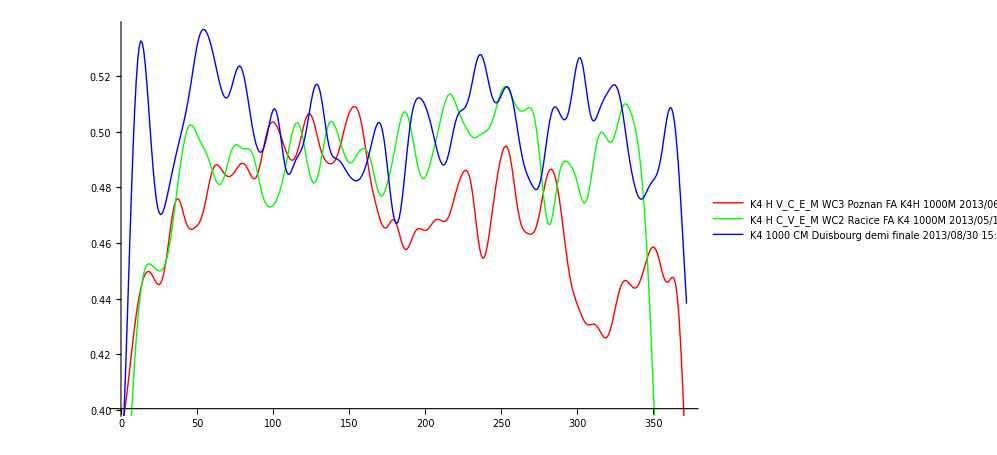

```mathematica
harmonicsPower[data_]:=Module[{datg,transg,noiseg},
datg=normalizeall[data];
transg=normalizevalues[Abs[Map[FourierDCT,datg]]];
noiseg=(*Transpose[{Table[i,{i,Length[datg]}],*)applylowpassfilter[Map[Norm,transg[[All,2;;]]]/transg[[All,1]],2]
(*}]*)
;
Return[noiseg]
]
nstrokesmoothing=10;
ListPlot[{
applylowpassfilter[harmonicsPower[getData[dataproc,1,"Forward Acceleration (Stroke)"]],nstrokesmoothing],
applylowpassfilter[harmonicsPower[getData[dataproc,2,"Forward Acceleration (Stroke)"]],nstrokesmoothing],
applylowpassfilter[harmonicsPower[getData[dataproc,3,"Forward Acceleration (Stroke)"]],nstrokesmoothing]},PlotStyle->{Red,Green,Blue},Joined->True,PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

```mathematica
getData[dataproc]
```

```mathematica
Module[{datg,datd,transg,transd,noiseg,noised},
datg=Take[normalizeall[getData[dataproc,3,"Forward Acceleration (Stroke)"]],{1,-1,2}];
datd=Take[normalizeall[getData[dataproc,3,"Forward Acceleration (Stroke)"]],{2,-1,2}];
transg=normalizevalues[Abs[Map[FourierDCT,datg]]];
noiseg=Transpose[{applylowpassfilter[Map[Norm,transg[[All,2;;]]]/transg[[All,1]],4],Table[i,{i,Length[datg]}]}];
transd=normalizevalues[Abs[Map[FourierDCT,datd]]];
noised=Transpose[{applylowpassfilter[Map[Norm,transd[[All,2;;]]]/transd[[All,1]],4],Table[i,{i,Length[datd]}]}];
GraphicsGrid[
{{
ListDensityPlot[datg,ImageSize->{400,600},AspectRatio->Length[ datg]/200,ColorFunction-> "TemperatureMap"],
ListDensityPlot[datd,ImageSize->{400,600},AspectRatio->Length[ datg]/200,ColorFunction-> "TemperatureMap"],
ListPlot[{noiseg,noised},ImageSize->{400,600},AspectRatio->Length[ datg]/200,Joined->True]
}}
]
]
```

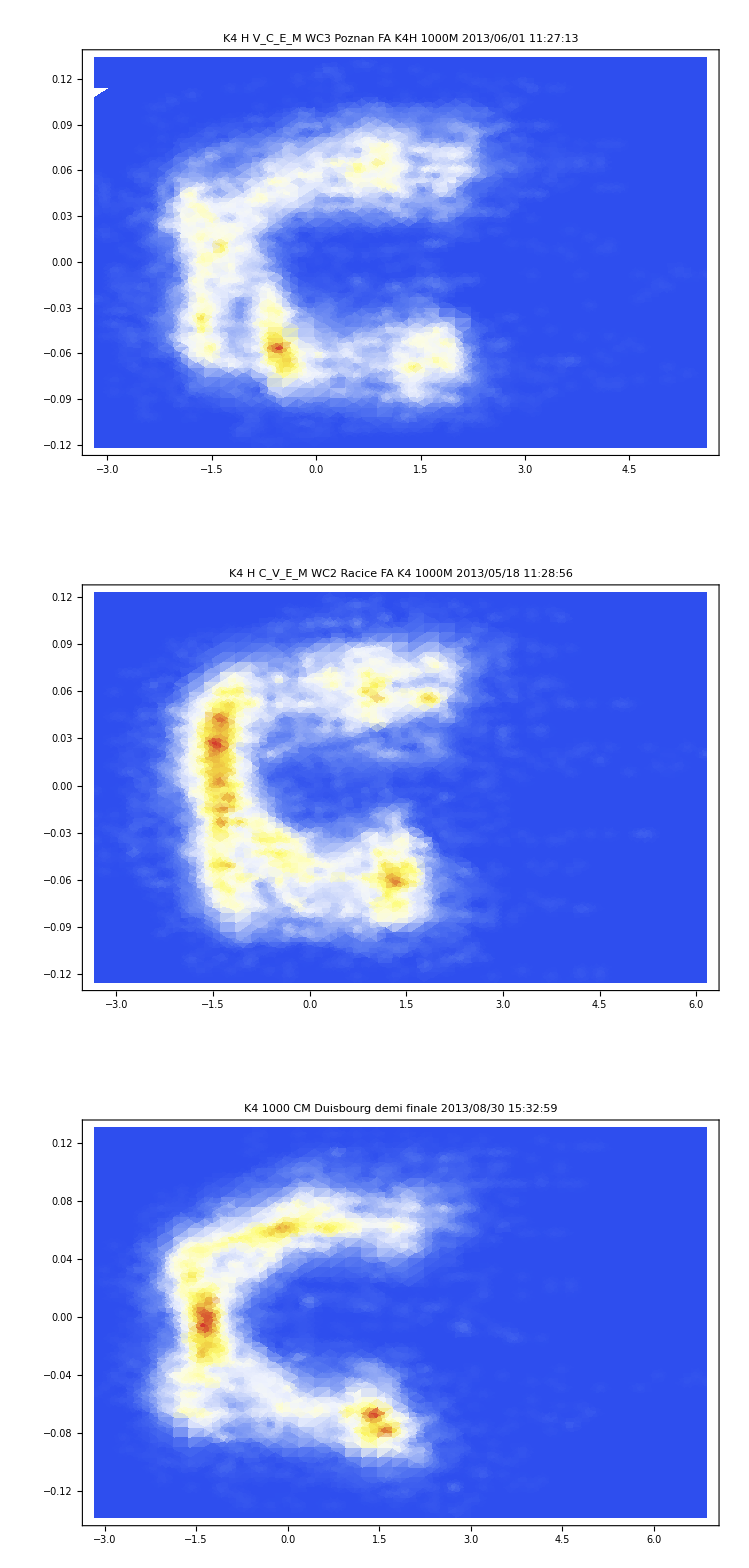

```mathematica
serie=3;
GraphicsGrid[Transpose[{Table[
SmoothDensityHistogram[Transpose[{getData[dataproc,serie,"Forward Acceleration"],applyhighpassfilter[getData[dataproc,serie,"Roll Angle"],150]}],{0.001,0.001},ColorFunction->"TemperatureMap",PlotRange->{All,All},PlotLabel->Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]][[serie]]],{serie,1,3}]}]]
```

```mathematica
SmoothDensityHistogram[Transpose[{getData[dataproc,2,"Pitch Angle"],getData[dataproc,2,"Forward Acceleration"]}],{0.0001,0.001},ColorFunction->"TemperatureMap",PlotRange->{{-0.01,0.01},{-3,4}}]
```

```mathematica
SmoothDensityHistogram[Transpose[{getData[dataproc,1,"Pitch Angle"],getData[dataproc,1,"Forward Acceleration"]}],{0.00005,0.01},ColorFunction->"TemperatureMap",PlotRange->{{-0.01,0.01},{-3.,5.}}]
```

```mathematica
SmoothDensityHistogram[Transpose[{getData[dataproc,1,"Roll Angle"],getData[dataproc,1,"Forward Acceleration"]}],{0.001,0.01},ColorFunction->"TemperatureMap",PlotRange->{{-0.2,0.2},{-3.,5.}}]
SmoothDensityHistogram[Transpose[{getData[dataproc,2,"Roll Angle"],getData[dataproc,2,"Forward Acceleration"]}],{0.001,0.01},ColorFunction->"TemperatureMap",PlotRange->{{-0.2,0.2},{-3.,5.}}]
```

```mathematica
Export["/Users/Vincent/Downloads/K4 H C_V_E_M 6108 201305181128 K4H1000M FA.avi",
Table[
Show[


SmoothDensityHistogram[

Take[Transpose[{getData[dataproc,1,"Roll Angle"],getData[dataproc,1,"Forward Acceleration"]}],
{x,x+1000}]
,{0.005,0.05},ColorFunction->"TemperatureMap",PlotRange->{{-0.2,0.2},{-3.,5.}}]


,

Graphics[Text[
ToString[Round[getData[dataproc,1,"Forward Distance"][[x]]]]<>" m",{0,5.5},{0,0}]],

PlotRange->{{-0.2,0.2},{-3.,6.}}

],

{x,1,Length[getData[dataproc,1,"Roll Angle"]]-1000,10}
]]
```

```mathematica
ListPlot[
{
Transpose[{getData[dataproc,1,"Forward Distance"],getData[dataproc,1,"Forward Velocity"]}],
Transpose[{getData[dataproc,2,"Forward Distance"],getData[dataproc,2,"Forward Velocity"]}]
},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{{0,100},{0,7}}]
```

```mathematica
Manipulate[ListPlot[
{getData[dataproc,1,"Forward Velocity"],
Take[getData[dataproc,2,"Forward Velocity"],{deb2,-1}],
Take[getData[dataproc,1,"Forward Velocity"],{deb3,-1}]
},Joined->True,PlotStyle->{Red,Green,Blue},PlotRang!e->{0,7}],
{deb2,1,400,1},{deb3,1,400,1}]
```

```mathematica
ListPlot[{applylowpassfilter[getData[dataproc,1,"Total Friction Force"],10]},PlotRange->All]
```

```mathematica
getAttribute[dataproc,1,"Mass"]
```

```mathematica
Module[{a,b,fit},
fit=FindFit[Transpose[{getData[dataproc,1,"Forward Velocity"],-getAttribute[dataproc,1,"Mass"]*getData[dataproc,1,"Forward Acceleration"]}],a*v+b*v^2,{a,b},v];
Print["Empirical Friction Linear Coefficient"->(a/.fit)];
Print["Empirical Friction Quadratic Coefficient"->(b/.fit)];

];
```

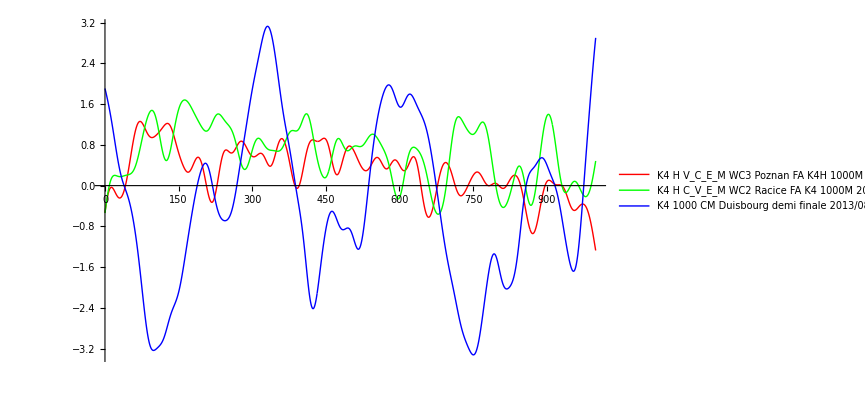

```mathematica
name="Roll Angle";
filteringTime=5;
ListPlot[{
applylowpassfilter[getData[dataproc,1,name]*180/π,filteringTime*100],
applylowpassfilter[getData[dataproc,2,name]*180/π,filteringTime*100],
applylowpassfilter[getData[dataproc,3,name]*180/π,filteringTime*100]
}
,PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]
,PlotStyle->{Red,Green,Blue},Joined->True,PlotRange->{All,All},DataRange->{0,1000}]
```

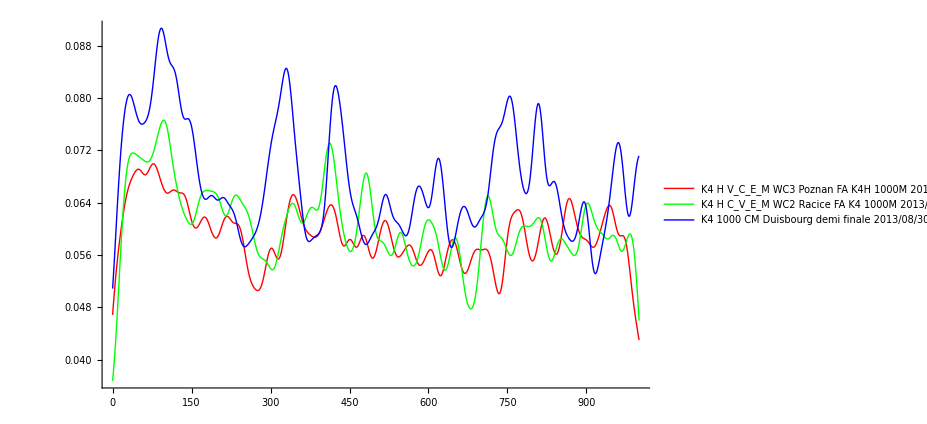

```mathematica
name="Roll Angle";
filteringTime=4;
ListPlot[{
Sqrt[applylowpassfilter[getData[dataproc,1,name]^2,filteringTime*100]],
Sqrt[applylowpassfilter[getData[dataproc,2,name]^2,filteringTime*100]],
Sqrt[applylowpassfilter[getData[dataproc,3,name]^2,filteringTime*100]]
}
,PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]
,PlotStyle->{Red,Green,Blue},Joined->True,PlotRange->{All,All},DataRange->{0,1000}]
```

```mathematica
SmoothDensityHistogram[Transpose[{applylowpassfilter[ Abs[getData[dataproc,2,"Roll Angular Velocity"]]+10*Abs[getData[dataproc,2,"Roll Angle"]],10],applylowpassfilter[getData[dataproc,2,"Forward Velocity"],10]}],{0.001,0.01},ColorFunction->"TemperatureMap",PlotRange->{{0.,2},{0.,8.}}]
```

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Acceleration Power"],200]}],
Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Friction Power"],200]}],
Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Power"],200]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]

ListPlot[
{

Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Acceleration Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Friction Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Power"],200]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]

ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Power"],200]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]
```

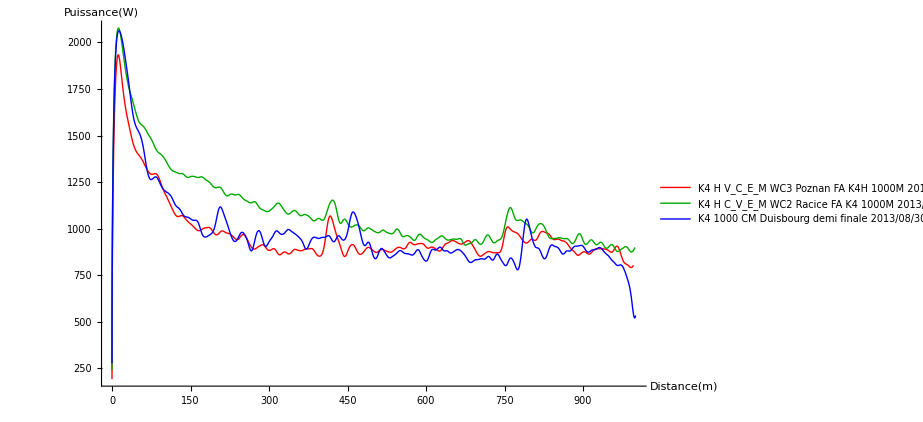

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Power"],200]}],
Transpose[{getData[dataproc,3,"Forward Distance"],
applylowpassfilter[getData[dataproc,3,"Total Power"],200]}]

},
PlotStyle->{Red,Darker[Green],Blue},
Joined->True,PlotRange->{All,All}, AxesLabel->{"Distance(m)","Puissance(W)"} ,PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

```mathematica
n=1;
f=20;
ListPlot[
{
Transpose[{getData[dataproc,n,"Forward Distance"],
applylowpassfilter[getData[dataproc,n,"Total Power"],f]}],
Transpose[{getData[dataproc,n,"Forward Distance"],
applylowpassfilter[getData[dataproc,n,"Acceleration Power"],f]}],
Transpose[{getData[dataproc,n,"Forward Distance"],
applylowpassfilter[getData[dataproc,n,"Total Friction Power"],f]}]
},
PlotStyle->{Red,Darker[Yellow],Darker[Green],Darker[Cyan],Blue,Magenta},
Joined->True,PlotRange->{{0,200},All}]
```

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Total Power"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Total Power"],200]}],
Transpose[{getData[dataproc,3,"Forward Distance"],
applylowpassfilter[getData[dataproc,3,"Total Power"],200]}],
Transpose[{getData[dataproc,4,"Forward Distance"],
applylowpassfilter[getData[dataproc,4,"Total Power"],200]}],
Transpose[{getData[dataproc,5,"Forward Distance"],
applylowpassfilter[getData[dataproc,5,"Total Power"],200]}],
Transpose[{getData[dataproc,6,"Forward Distance"],
applylowpassfilter[getData[dataproc,6,"Total Power"],200]}]

},
PlotStyle->{Red,Darker[Yellow],Darker[Green],Darker[Cyan],Blue,Magenta},
Joined->True,PlotRange->{All,All},PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,3,"Forward Distance"],
applylowpassfilter[getData[dataproc,3,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,4,"Forward Distance"],
applylowpassfilter[getData[dataproc,4,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,5,"Forward Distance"],
applylowpassfilter[getData[dataproc,5,"Forward Velocity"],200]}],
Transpose[{getData[dataproc,6,"Forward Distance"],
applylowpassfilter[getData[dataproc,6,"Forward Velocity"],200]}]

},
PlotStyle->{Red,Darker[Yellow],Darker[Green],Darker[Cyan],Blue,Magenta},
Joined->True,PlotRange->{All,All},PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[power[getData[dataproc,1,"Forward Velocity"],getData[dataproc,1,"Forward Acceleration"]],200]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[power[getData[dataproc,2,"Forward Velocity"],getData[dataproc,2,"Forward Acceleration"]],200]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]
```

```mathematica
TableForm[getData[dataproc]]
```

```mathematica
n=8;
GraphicsGrid[{Table[
DensityHistogram[Transpose[{

applylowpassfilter[getData[dataproc,n,"Roll Angle"],1],applylowpassfilter[getData[dataproc,n,"Forward Acceleration"],1]

}],{100,100},ColorFunction->"TemperatureMap",PlotRange->All,ImageSize->{320,320}],{n,3,6}],
Table[
DensityHistogram[Transpose[{

applylowpassfilter[getData[dataproc,n,"Roll Angle"],1],applylowpassfilter[getData[dataproc,n,"Forward Acceleration"],1]

}],{100,100},ColorFunction->"TemperatureMap",PlotRange->All,ImageSize->{320,320}],{n,7,10}]
}]
```

```mathematica
getData[dataproc]
```

```mathematica
n=6;
xdat=getData[dataproc,n,"Roll Angle"]*180/π;
ydat1=applylowpassfilter[getData[dataproc,n,"Total Friction Power"],1];
ydat2=applylowpassfilter[getData[dataproc,n,"Acceleration Power"],1];
ydat3=applylowpassfilter[getData[dataproc,n,"Total Power"],1];
dur=(getData[dataproc,n,"Time"][[-1]]-getData[dataproc,n,"Time"][[1]]);

Animate[ListPlot[
{
Transpose[{Take[xdat,{i,i+20}],Take[ydat1,{i,i+20}]}],
Transpose[{Take[xdat,{i,i+20}],Take[ydat2,{i,i+20}]}],
Transpose[{Take[xdat,{i,i+20}],Take[ydat3,{i,i+20}]}]
}
,Joined->True,PlotStyle->{Red,Darker[Green],Blue},PlotRange->{{-12,12},{-8000,10000}},ImageSize->{640,480}],{i,1,Length[xdat-20],1},DefaultDuration->dur]
```

```mathematica
normalizeall[getData[dataproc,1,"Forward Acceleration (Stroke)"]]
```

```mathematica
"Forward Acceleration Garbage Rate"
```

```mathematica
n=1;
scheme="GrayTones";
DensityHistogram[Transpose[{

getData[dataproc,n,"Stroke Phase"],applyhighpassfilter[getData[dataproc,n,"Forward Velocity"],100]

}],{100,300},ColorFunction->(ColorData[scheme][0.+2.*#]&),PlotRange->All,Background->ColorData[scheme][0.],ImageSize->{640,640}]
```

```mathematica
ListPlot[
{

Transpose[{getData[dataproc,1,"Forward Distance"],
applylowpassfilter[getData[dataproc,1,"Forward Acceleration Garbage Rate"],2]}],
Transpose[{getData[dataproc,2,"Forward Distance"],
applylowpassfilter[getData[dataproc,2,"Forward Acceleration Garbage Rate"],2]}]

},
PlotStyle->{Red,Green,Blue},
Joined->True,PlotRange->{All,All}]
```

```mathematica
x="Forward Velocity";
y="Right Velocity";
z="Up Velocity";
n=70;
cutoff=100;


serie1=1;
serie2=2;
serie3=3;

xmin=Min[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
xmax=Max[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
ymin=Min[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
ymax=Max[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
zmin=Min[applyhighpassfilter[getData[dataproc,serie1,z],cutoff]];
zmax=Max[applyhighpassfilter[getData[dataproc,serie1,z],cutoff]];

xmin=-0.3;
xmax=0.3;
ymin=-0.3;
ymax=0.3;
zmin=-0.3;
zmax=0.3;


ref=Table[1,{n},{n},{n}];

res1=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie1,x],cutoff],
applyhighpassfilter[getData[dataproc,serie1,y],cutoff],
applyhighpassfilter[getData[dataproc,serie1,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res1=res1/Max[res1];


res2=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie2,x],cutoff],
applyhighpassfilter[getData[dataproc,serie2,y],cutoff],
applyhighpassfilter[getData[dataproc,serie2,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res2=res2/Max[res2];


res3=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie3,x],cutoff],
applyhighpassfilter[getData[dataproc,serie3,y],cutoff],
applyhighpassfilter[getData[dataproc,serie3,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res3=res3/Max[res3];

res=Outer[Times,res1,{10,0,0,0}]+Outer[Times,res2,{0,10,0,0}]+Outer[Times,res3,{0,0,10,0}]+Outer[Times,res1^2+res2^2+res3^2,{0,0,0,5}];

Image3D[res,Background->Black]
```

```mathematica
x="Total Force";
y="Roll Angle";
z="Distance Corrected";
n=80;
cutoff=100;


serie1=1;
serie2=2;
serie3=1;

PrintTemporary["OK0"];

xmin=Min[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
xmax=Max[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
ymin=Min[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
ymax=Max[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
zmin=Min[getData[dataproc,serie1,z]];
zmax=Max[getData[dataproc,serie1,z]];

(*xmin=-0.3;
xmax=0.3;*)
ymin=-0.1;
ymax=0.1;
zmin=0;
zmax=1000;


ref=Table[1,{n},{n},{n}];

res1=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie1,x],cutoff],
applyhighpassfilter[getData[dataproc,serie1,y],cutoff],
getData[dataproc,serie1,z]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res1=res1/Max[res1];
PrintTemporary["OK1"];

res3=res1;

res2=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie2,x],cutoff],
applyhighpassfilter[getData[dataproc,serie2,y],cutoff],
getData[dataproc,serie2,z]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res2=res2/Max[res2];

(*
res3=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie3,x],cutoff],
applyhighpassfilter[getData[dataproc,serie3,y],cutoff],
applyhighpassfilter[getData[dataproc,serie3,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res3=res3/Max[res3];*)


res=Outer[Times,res1,{10,0,0,0}]+Outer[Times,res2,{0,10,0,0}]+Outer[Times,res3,{0,0,10,0}]+Outer[Times,res1^2+res2^2+res3^2,{0,0,0,3}];
PrintTemporary["OK2"];
Image3D[res,Background->Black]
```

```mathematica
x="Forward Acceleration";
y="Roll Angle";
z="Forward Velocity";
n=70;
cutoff=100;


serie1=1;
serie2=2;
serie3=3;

xmin=Min[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
xmax=Max[applyhighpassfilter[getData[dataproc,serie1,x],cutoff]];
ymin=Min[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
ymax=Max[applyhighpassfilter[getData[dataproc,serie1,y],cutoff]];
zmin=Min[applyhighpassfilter[getData[dataproc,serie1,z],cutoff]];
zmax=Max[applyhighpassfilter[getData[dataproc,serie1,z],cutoff]];
(*
xmin=-1;
xmax=1;
ymin=-0.3;
ymax=0.3;
zmin=-0.3;
zmax=0.3;
*)


ref=Table[1,{n},{n},{n}];

res1=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie1,x],cutoff],
applyhighpassfilter[getData[dataproc,serie1,y],cutoff],
applyhighpassfilter[getData[dataproc,serie1,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res1=res1/Max[res1];


res2=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie2,x],cutoff],
applyhighpassfilter[getData[dataproc,serie2,y],cutoff],
applyhighpassfilter[getData[dataproc,serie2,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res2=res2/Max[res2];


res3=BinCounts[Transpose[{
applyhighpassfilter[getData[dataproc,serie3,x],cutoff],
applyhighpassfilter[getData[dataproc,serie3,y],cutoff],
applyhighpassfilter[getData[dataproc,serie3,z],cutoff]
}],
{xmin,xmax,(xmax-xmin)/n},
{ymin,ymax,(ymax-ymin)/n},
{zmin,zmax,(zmax-zmin)/n}];
res3=res3/Max[res3];

res=Outer[Times,res1,{10,0,0,0}]+Outer[Times,res2,{0,10,0,0}]+Outer[Times,res3,{0,0,10,0}]+Outer[Times,res1^2+res2^2+res3^2,{0,0,0,1}];

Image3D[res,Background->Black]
With[{i=Image3D[res],size=n},
Manipulate[Grid[{#&/@{
Show[Image3DSlices[i,{s},1][[1]],Graphics[{Red,Line[{{c,0},{c,size}}],Line[{{0,size-r+1},{size,size-r+1}}]}],ImageSize->{320,320}],
Show[Image3DSlices[i,{r},2][[1]],Graphics[{Red,Line[{{c,0},{c,size}}],Line[{{0,size-s+1},{size,size-s+1}}]}],ImageSize->{320,320}],
Show[Image3DSlices[i,{c},3][[1]],Graphics[{Red,Line[{{r,0},{r,size}}],Line[{{0,size-s+1},{size,size-s+1}}]}],ImageSize->{320,320}]}}],
{s,1,size,1},{r,1,size,1},{c,1,size,1}]]
```

-Graphics3D-

```mathematica
ListVectorPlot3D[
Take[
Transpose[
{
{
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Forward Velocity"],cutoff]],
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Right Velocity"],cutoff]],
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Up Velocity"],cutoff]]
},{
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Forward Acceleration"],cutoff]],
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Right Acceleration"],cutoff]],
Standardize[applyhighpassfilter[getData[dataproc,serie1,"Up Acceleration"],cutoff]]
}
},
{2,3,1}
]
,
{1000,1100}
],
VectorPoints->10,
PlotRange->All
]
```

-Graphics3D-

```mathematica
Plot3D[Max[res1,res2],{res1,0,1},{res2,0,1}]
Plot3D[Min[res1,res2],{res1,0,1},{res2,0,1}]
Plot3D[1-(1-res1)*(1-res2),{res1,0,1},{res2,0,1}]
Plot3D[res1*res2,{res1,0,1},{res2,0,1}]
Plot3D[res1^2+res2^2,{res1,0,1},{res2,0,1}]
```

```mathematica
x="Forward Acceleration";
y="Right Acceleration";
z="Up Acceleration";
f="Forward Velocity";
serie=1;
opacity=0.5;
ListContourPlot3D[Transpose[{
Standardize[getData[dataproc,serie,x]],
Standardize[getData[dataproc,serie,y]],
getData[dataproc,serie,z],
power[getData[dataproc,serie,"Forward Velocity"],getData[dataproc,serie,"Forward Acceleration"]]
}],Contours->6,Mesh->None,BoundaryStyle->None,ContourStyle->{Opacity[opacity,Red],Opacity[opacity,Yellow],Opacity[opacity,Green],Opacity[opacity,Cyan],Opacity[opacity,Blue],Opacity[opacity,Magenta]},PlotRange->All,MaxPlotPoints->100,AxesLabel->{x,y,z}]
```

```mathematica
x="Pitch Angular Velocity";
y="Roll Angular Velocity";
z="Yaw Angular Velocity";
```

```mathematica
x="Forward Acceleration";
y="Right Acceleration";
z="Up Acceleration";
f="Forward Acceleration";
serie=1;
ListContourPlot3D[Transpose[{
Standardize[getData[dataproc,serie,x]],
Standardize[getData[dataproc,serie,y]],
Standardize[getData[dataproc,serie,z]],
Standardize[getData[dataproc,serie,f]]
}],Contours->6,Mesh->None,ContourStyle->{Red,Yellow,Green,Cyan,Blue,Magenta},PlotRange->All,MaxPlotPoints->80,AxesLabel->{x,y,z}]
```

```mathematica
x="Roll Angle";
y="Pitch Angle";
z="Yaw Angle";
f="Forward Acceleration";
serie=1;
ListContourPlot3D[Transpose[{
Standardize[getData[dataproc,serie,x]],
Standardize[getData[dataproc,serie,y]],
Standardize[getData[dataproc,serie,z]],
Standardize[getData[dataproc,serie,f]]
}],Contours->6,Mesh->None,ContourStyle->{Red,Yellow,Green,Cyan,Blue,Magenta},PlotRange->All,MaxPlotPoints->80,AxesLabel->{x,y,z}]
```

```mathematica
Plot[(1-Cos[x])/2,{x,0,2*π}]
```

```mathematica
f1[x_]:=(((1-Cos[x])/2)^8)*2-0.3;
f2[x_]:=((1-Cos[x])/2)^0.2-0.3;
Plot[{f1[x],f2[x]},{x,0,2*π}]
```

```mathematica
temp=Take[normalizeall[getData[dataproc,1,"Forward Acceleration (Stroke)"]],{1,-1,1}];
temp2=Take[normalizeall[getData[dataproc,1,"Roll Angle (Stroke)"]],{1,-1,1}];
res=Table[Correlation[temp[[i]],temp[[j]]],{i,1,Length[temp]},{j,1,Length[temp]}];
res2=Table[Correlation[temp2[[i]],temp2[[j]]],{i,1,Length[temp2]},{j,1,Length[temp2]}];
```

```mathematica
ListDensityPlot[res,DataRange->All,ColorFunction->"TemperatureMap"]
ListDensityPlot[res2,DataRange->All,ColorFunction->"TemperatureMap"]
```

-Graphics-

```mathematica
ListPlot[getData[dataproc,1,"Forward Acceleration Garbage Rate (Stroke)"],Joined->True,PlotRange->All]
```

-Graphics-

```mathematica
RGBColor@ColorConvert[Join[{1.},Take[ColorConvert[Hue[0.5],"LUV"],{2,3}]],"LUV"->"RGB"]
```

RGBColor[{0.0911189,1.24545,1.24545}]

```mathematica
ListPlot[Table[Power[6+applylowpassfilter[Log[1-getData[dataproc,i,"Forward Acceleration Garbage Rate (Stroke)"]],10],-0.1],{i,1,Length[getData[dataimport]]}],Joined->True,PlotRange->{All,All}, AxesLabel->{"Stroke","Deviation"} ,PlotStyle->Table[RGBColor@ColorConvert[Join[{.8},Take[ColorConvert[Hue[h],"LAB"],{2,3}]],"LAB"->"RGB"],{h,0,1,1/Length[getData[dataimport]]}],PlotLegends->Placed[LineLegend[Automatic,Map[Function[x,Apply[List,x]],getData[dataproc]][[All,1]],LegendLayout->"Column"],Bottom]]
```

-Graphics-

```mathematica
strokes=normalizeall[getData[dataproc,1,"Roll Angle (Stroke)"]];
meanstroke=Mean[strokes];
res=Table[N[Correlation[strokes[[i]],meanstroke]],{i,Length[strokes]}];
res[[1]]=0;
res[[-1]]=0;
```

```mathematica
ListPlot[Log[1-res],Joined->True,PlotRange->All]
```

-Graphics-